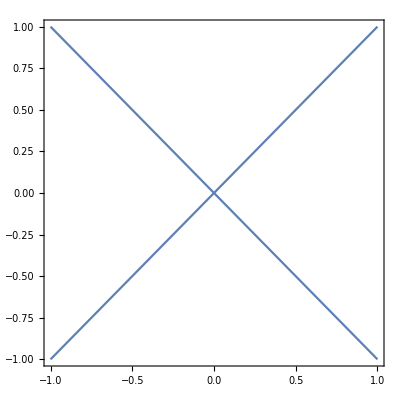

```mathematica
ContourPlot[(y-x)*(y+x)==0,{x,-1,1},{y,-1,1},PlotPoints->50]
```

```mathematica
RectArr = Drop[
{
{0.4011108,0.74725069,0.5988892,0.25274931,0.09546704},
{0.31817939,0.43961431,0.68182061,0.30763638,0.08521775},
{0.44480138,0.14970917,0.55519862,0.28990514,0.07440806},
{0.,0.74725069,0.4011108,0.25274931,0.06523844},
{0.36735339,0.,0.63264661,0.19464034,0.05828913},
{0.,0.3645502,0.4011108,0.38270049,0.05333428},
{0.,0.19464034,0.44480138,0.16990985,0.04860915},
{0.,0.,0.36735339,0.19464034,0.03879012}
}
,None,-1];
n = RectArr//Length;
```

```mathematica
area = Sum[RectArr[[i,3]]*RectArr[[i,4]],{i,1,n}]
```

1.04718

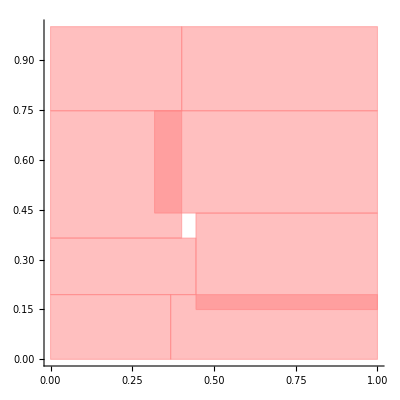

```mathematica
Graphics[Table[
{EdgeForm[Dashed],Opacity[0.5],Pink,
Rectangle[
{RectArr[[i,1]],RectArr[[i,2]]},
{RectArr[[i,1]]+RectArr[[i,3]],
RectArr[[i,2]]+RectArr[[i,4]]}]
},{i,1,n}],Axes->True]
```